```mathematica
(* Average jump length as function of m *)
Clear[m,r];
Assuming[{m>0},
Integrate[r^2 Exp[-m r],{r,0,∞}]/Integrate[r Exp[-m r],{r,0,∞}]]
```

```mathematica
(* Upper (f) and lower (g) branches of the LambertW *)
f[x_]:=t/.Last[FindRoot[t E^-t-x,{t,2}]];
g[x_]:=t/.First[FindRoot[t E^-t-x,{t,0}]];
```

```mathematica
Plot[{1,f[x],g[x]},{x,0,1/E}]
```

## The real deal

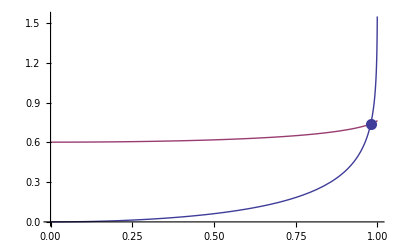

```mathematica
(*********************** 
     Set constants
**********************)
Clear[R,avjmp,m,λ];
Njumps=2000;
R=1;  (* cylinder radius *)
avjmp =2 R;  (* average length of the jumps = 2/m *)
m=2/avjmp;
eqλ=ξ *BesselJ[1,ξ R]*BesselK[0,R Sqrt[m^2-ξ^2]]-Sqrt[m^2-ξ^2]*BesselJ[0,ξ R]*BesselK[1,R Sqrt[m^2-ξ^2]];
λ=ξ/.First[FindRoot[eqλ,{ξ,m/100},AccuracyGoal->Infinity,PrecisionGoal->8]//Quiet];
c=Sqrt[m^2-λ^2];
(* Test solution for λ *)
Show[{
Plot[{x BesselJ[1,x R]*BesselK[0,R Sqrt[m^2-x^2]],Sqrt[m^2-x^2]BesselJ[0,x R]BesselK[1,R Sqrt[m^2-x^2]]},{x,0,m}],
ListPlot[{{λ,λ BesselJ[1,λ R]*BesselK[0,R Sqrt[m^2-λ^2]]}},PlotStyle->PointSize[.02]]
}(*,PlotRange->{{2,2.2},{0,.00005}}*)]
```

```mathematica
(* Set initial point *)
x=0;y=0; z=0;
pts={{x,y,z}};

counter=0;
While[counter<Njumps,
(*****************************
Generation new point x'
****************************)

(* Generation random uniform angles θ and ϕ *)
phi=RandomReal[2π];
costh=RandomReal[{-1,1}];

(* Generation r=|x'-x|^with truncated Gamma distribution *)
α=m-λ costh;   (* Always positive number *)
rho=Sqrt[x^2+y^2];
rstar=Sqrt[R^2+rho^2-2 R rho Cos[phi]]/Sqrt[1-costh^2];
β=1-(1+α rstar)Exp[-α rstar];
w=RandomReal[];
r=(t-1)/α/.Last[Quiet[FindRoot[t E^-t-(1-β w)/E,{t,2}]]];
xnew=x+r Sqrt[1-costh^2]Cos[phi];
ynew=y+r Sqrt[1-costh^2]Sin[phi];
znew=z+r costh;

(*Print["ϕ = ",phi/π," * π"];Print["Cos[θ] = ",costh]; Print["α = ", α];  Print["r_* = ", rstar];Print["β = ", β];  Print["r = ", r];*)

(*****************************
Rejection sampling
*****************************)
rhonew=Sqrt[xnew^2+ynew^2];
If[RandomReal[]<BesselJ[0,λ rhonew],
Module[{},
counter++;
x=xnew;y=ynew;z=znew;
pts=Join[pts,{{x,y,z}}];
]
];

]
Export["Projects/Paths/repo_alb/main/output/cylinder.dat",pts];
```

Export::nodir: Directory "/home/alberto/output/" does not exist.

OpenWrite::noopen: Cannot open "/home/alberto/output/cylinder.dat".

```mathematica
Graphics3D[Line[pts]]
```